# Лабораторная работа 5. Рекурсия

Выполнила студентка ММФ БГУ
  КМ, 1 к, 5 гр. Шклярик В.С.
 6 октября 2021

## 1. Построение дерева выражения

### Задание 2.1

```mathematica
ExprAsTree[expr_,options___Rule]:=Graphics[ExprAsTree[expr,{0,0}],options]
```

```mathematica
ExprAsTree[atom_?AtomQ,coord:{_,_}]:=Text[atom,coord,Background->LightRed]
```

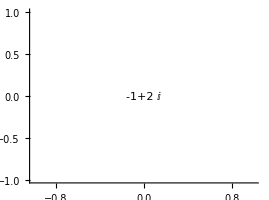

```mathematica
ExprAsTree[-1+2ⅈ,Axes->True,BaseStyle->{Medium, FontWeight->Bold}]
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:={Text[Head[expr],{x,y}]}
```

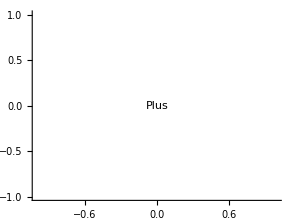

```mathematica
ExprAsTree[a+2ⅈ,Axes->True,BaseStyle->{Large,FontWeight->Bold}]
```

```mathematica
ClearAll[Width];
Width[_?AtomQ]=1;
Width[expr_]:=Plus@@Width/@List@@(expr)
```

```mathematica
expr=1/(a^5+b)-x^9+57-v
```

```mathematica
Width/@List@@(expr)
```

{1,4,2,3}

```mathematica
FoldList[Plus,0,Width/@List@@(expr)]//Most
```

{0,1,5,7}

```mathematica
{x+#,y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most
```

{{x,-1+y},{1+x,-1+y},{5+x,-1+y},{7+x,-1+y}}

```mathematica
ClearAll[x,y]
```

```mathematica
NodesCoord[expr_,{x_,y_}]:={x+#,y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:={Text[Head[expr],{x,y}],MapThread[ExprAsTree[#1,#2]&,{List@@(expr),NodesCoord[expr,{x,y}]}]}
```

```mathematica
ExprAsTree[expr,{1,1}]
```

{Text[Plus,{1,1}],{Text[57,{1,0}],{Text[Power,{2,0}],{{Text[Plus,{2,-1}],{{Text[Power,{2,-2}],{Text[a,{2,-3}],Text[5,{3,-3}]}},Text[b,{4,-2}]}},Text[-1,{5,-1}]}},{Text[Times,{6,0}],{Text[-1,{6,-1}],Text[v,{7,-1}]}},{Text[Times,{8,0}],{Text[-1,{8,-1}],{Text[Power,{9,-1}],{Text[x,{9,-2}],Text[9,{10,-2}]}}}}}}

```mathematica
Table[Level[expr,{i}],{i,1,Depth[expr]-1}]
```

{{57,1/(a^5+b),-v,-x^9},{a^5+b,-1,-1,v,-1,x^9},{a^5,b,x,9},{a,5}}

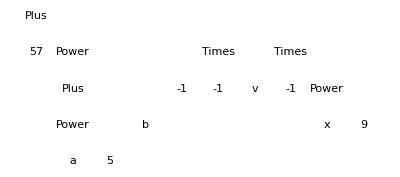

```mathematica
ExprAsTree[expr, BaseStyle->{Medium,FontWeight->Bold}]
```

```mathematica
g[expr_,{x_,y_}]:=Graphics[{Green,Line[MapThread[List,{Table[{x,y},Length[NodesCoord[expr,{x,y}]]],NodesCoord[expr,{x,y}]}]]}]
```

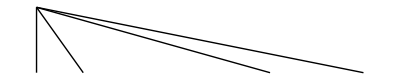

```mathematica
g[expr,{0,2}]
```

```mathematica
ExprAsTree[expr_,{x_,y_}]:={{Pink,Line[MapThread[List,{Table[{x,y},Length[NodesCoord[expr,{x,y}]]],NodesCoord[expr,{x,y}]}]]},Text[Tooltip[Head[expr],(expr)],{x,y},Background->LightPurple],MapThread[ExprAsTree[#1,#2]&,{List@@(expr),NodesCoord[expr,{x,y}]}]}
```

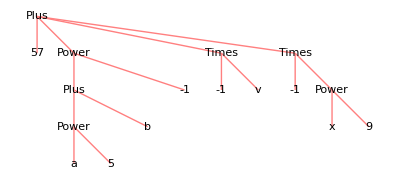

```mathematica
ExprAsTree[expr, BaseStyle->{Medium,FontWeight->Bold}]
```

### Новая функция с головой посередине.

```mathematica
NodesCoord2[expr_,{x_,y_}]:={x+#,y-1}&/@FoldList[Plus,0,Width/@List@@(expr)]//Most
```

```mathematica
ExprAsTree2[expr_,options___Rule]:=Graphics[ExprAsTree2[expr,{0,0}],options]
```

```mathematica
ExprAsTree2[atom_?AtomQ,coord:{_,_}]:=Text[atom,coord,Background->LightRed]
```

```mathematica
ExprAsTree2[expr_,{x_,y_}]:={Text[Head[expr],{x,y}]}
```

```mathematica
ExprAsTree2[expr_,{x_,y_}]:={Text[Head[expr],{x,y}],MapThread[ExprAsTree2[#1,#2]&,{List@@(expr),NodesCoord2[expr,{x,y}]}]}
```

```mathematica
NodesCoord2[expr,{0,1.2}]//Last
```

{7,0.2}

```mathematica
ExprAsTree2[expr_,{x_,y_}]:={{Pink,Line[MapThread[List,{Table[{x,y},Length[NodesCoord2[expr,{x,y}-1/2(NodesCoord2[expr,{0,1.2}]//Last)]]],NodesCoord2[expr,{x,y}-1/2(NodesCoord2[expr,{0,1.2}]//Last)]}]]},Text[Tooltip[Head[expr],(expr)],{x,y},Background->LightPurple],MapThread[ExprAsTree2[#1,#2]&,{List@@(expr),NodesCoord2[expr,{x,y}-1/2(NodesCoord2[expr,{0,1.2}]//Last)]}]}
```

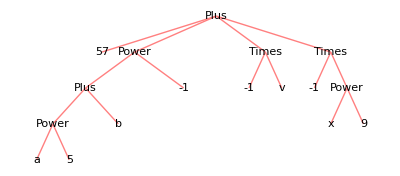

```mathematica
ExprAsTree2[expr, BaseStyle->{Medium,FontWeight->Bold}]
```

## 2. Рекурсия. Числа Фибоначчи и функция Аккермана.

### Последовательность чисел Фибоначчи

```mathematica
f[0]=0;
f[1]=1;
f[x_]:=f[x]=f[x-1]+f[x-2]
```

```mathematica
f[7]
```

13

```mathematica
?f
```

```mathematica
FibonacciSequence[n_]:=FibonacciSequence[n]=Table[f[i],{i,0,n}]
```

```mathematica
FibonacciSequence[16]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987}

```mathematica
?FibonacciSequence
```

### Значения функции Аккермана

```mathematica
Ackerman[0,n_]:=Ackerman[0,n]=n+1;
Ackerman[m_,0]:=Ackerman[m,0]=Ackerman[m-1,1];
Ackerman[m_,n_]:=Ackerman[m,n]=Ackerman[m-1,Ackerman[m,n-1]]
```

```mathematica
Ackerman[3,1]
```

13

```mathematica
ListPlot3D[Table[Ackerman[m,n],{m,0,2},{n,0,10}]]
```

-Graphics3D-